## Profile functions in the steady flow (fully resolved)

This notebook plots the profile functions for u, w and q obtained from the full system at two different x values.

```mathematica
(* clear the scope *)
Quiet[Remove["Global`*"];Remove["FreeSurf`*"]]
```

```mathematica
(* set directory of the engine folder *)
engineDirectory=FileNameJoin[{ParentDirectory[NotebookDirectory[]],"engine"}];
```

```mathematica
(* load engine *)
Get[FileNameJoin[{engineDirectory,"FreeSurf.wl"}]]
```

```mathematica
(* just some option for nicer plots *)
SetOptions[$FrontEndSession,PrintingStyleEnvironment->"Working"];
```

```mathematica
(* create a legend *)
legend=LineLegend[ColorData[106,#]&/@{1,2,3},{"0.2","0.4","0.6"},LegendLabel->"H",
LabelStyle->{Directive[14],Black},LegendMargins->{{10, 20}, {20, 10}}]; (* create a legend *)
```

```mathematica
(* define input parameters *)
Fr=.6;n=90; η=.09; σ=.25;
xMin=-.2;xMax=.6;
```

```mathematica
(*Run simulation*)
{freeSurf0p2,freeSurf0p4,freeSurf0p6}=FreeSurf[#,Fr,η,σ,n]&/@{.2,.4,.6};
```

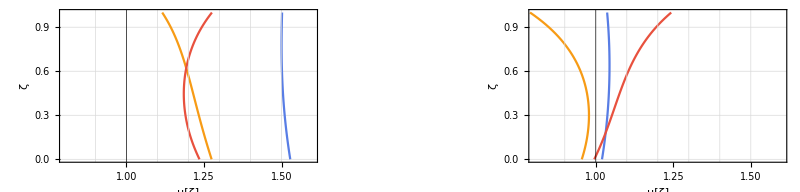

```mathematica
(* Extract and plot profile functions for horizontal velocity *)
{u0p2,u0p4,u0p6}={u[x,ζ] /.#,ζ}&/@{freeSurf0p2,freeSurf0p4,freeSurf0p6};
{pUxMin,pUxMax}=ParametricPlot[
Evaluate[{u0p2,u0p4,u0p6} /. x->#],{ζ,0,1},
PlotRange->{{.8,1.6},{0,1}},
AspectRatio->.5,
GridLines->{{.9,{1,Directive[Black,Thick]},1.1,1.2,1.3,1.4,1.5},Automatic},
GridLinesStyle->{Black,Opacity[1]},
FrameStyle->Black,
Frame->True,
FrameLabel->{"u[ζ]","ζ"},
PlotTheme->{"Frame","BoldColor","MediumLines"},
LabelStyle->{Directive[14],Black}
]&/@{xMin,xMax};
GraphicsRow[{pUxMin,legend,pUxMax}]
```

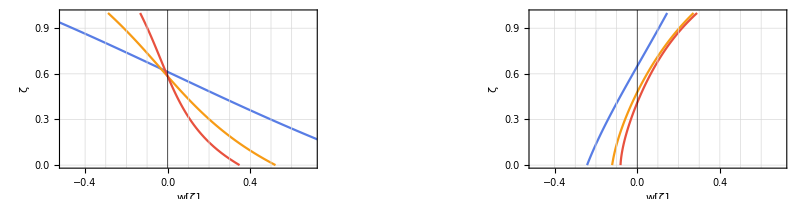

```mathematica
(* Extract and plot profile functions for vertical velocity *)
{w0p2,w0p4,w0p6}={w[x,ζ] /.#,ζ}&/@{freeSurf0p2,freeSurf0p4,freeSurf0p6};
{pWxMin,pWxMax}=ParametricPlot[
Evaluate[{w0p2,w0p4,w0p6} /. x->#],{ζ,0,1},
PlotRange->{{-.5,.7},{0,1}},
AspectRatio->.5,
Axes->False,
FrameStyle->Black,
FrameLabel->{"w[ζ]","ζ"},
GridLines->{{-.4,-.3,-.2,-.1,{0,Directive[Black,Thick]},.1,.2,.3,.4,.5,.6},Automatic},
GridLinesStyle->{Opacity[1],Black},
PlotTheme->{"Frame","BoldColor","MediumLines"},
LabelStyle->{Directive[14],Black}
]& /@ {xMin,xMax};
GraphicsRow[{pWxMin,legend,pWxMax}]
```

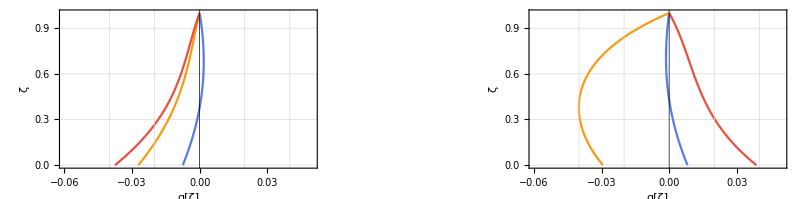

```mathematica
(* Extract and plot profile functions for nonhydrostatic pressure *)
{q0p2,q0p4,q0p6}={q[x,ζ] /.#,ζ}&/@{freeSurf0p2,freeSurf0p4,freeSurf0p6};
{pQxMin,pQxMax}=ParametricPlot[
Evaluate[{q0p2,q0p4,q0p6} /. x->#],{ζ,0,1},
PlotRange->{{-.06,0.05},{0,1}},
AspectRatio->.5,
Axes->False,
GridLines->{{-.04,-.02,{0,Directive[Black,Thick]},.02,.04},Automatic},
GridLinesStyle->{Black,Opacity[1]},
FrameStyle->Black,
FrameLabel->{"q[ζ]","ζ"},
PlotTheme->{"Frame","BoldColor","MediumLines"},
LabelStyle->{Directive[14],Black}
]& /@ {xMin,xMax};
GraphicsRow[{pQxMin,legend,pQxMax}]
```